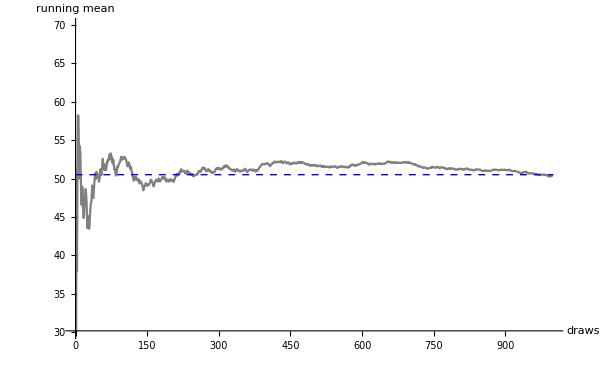

```mathematica
n = 1000;
vData=RandomVariate[DiscreteUniformDistribution[{1,100}],{n}];
vMean=Accumulate[vData]/Table[i,{i,1,n}];
Show[ListLinePlot[vMean,PlotRange->{Automatic,{30,70}},PlotStyle->Gray,Epilog->{Dashed,Blue,Line[{{0,50.5},{1000,50.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"draws ","running  mean "}],ImageSize->600]
```